```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/XXZ_model/"]
]
```

/Users/pwrzosek/Documents/GitHub/XXZ_model

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
```

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_",J,"_",tail,".json"];
sData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,sData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
anisotropyAvail=Normal[DeleteDuplicates[ds[Take,"anisotropy"]]];
<|"size"->sizeAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "anisotropy"->anisotropyAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_,n_]:=(
data=Apply[ds,directive];
x=(data[Take,keys[[1]]]//Normal);
y=(data[Take,keys[[2]]]//Normal);
z=(data[Take,keys[[3]]]//Normal);
zdim=Dimensions[z][[3]];
result={x[[1]],Append[y[[1]],0],Append[z[[1]],Table[0,zdim]]};
Clear[x,y,z];
result
)
```

```mathematica
getDensityPlot[spc_,n_]:=(
SetOptions[LinTicks,TickLengthScale->1.5];

plt=ListDensityPlot[Transpose[spc[[3]]],
DataRange->{{0-1/n,2+1/n}*Pi,{-3,7}},ImageSize->Medium,
Frame->True,Axes->False,
FrameStyle->Directive[Black,28,FontFamily->"Bookman Old Style"],
LabelStyle->Directive[Black,20],
InterpolationOrder->0,
ColorFunction->Function[x,Blend[{White,Lighter[Blue],Black},x]],(*ColorData[{"SunsetColors","Reverse"}]*)
PlotRange->{{0,2Pi},{-2,4},{0,1}},
PlotLegends->Placed[Automatic,Right],
ClippingStyle->Automatic,
AspectRatio->0.75,
FrameLabel->{"k","ω / t"},
Epilog->{
Text[
Style["",Black,24,FontFamily->"Bookman Old Style"],
{Pi/5.5,3.5}]
},
FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks[0,2Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)],StripTickLabels[LinTicks[0,2Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)]]}}
];

plt
)
```

```mathematica
makePlotsSpc[]:=(
dirc={Select[#coupling==J&&#size==n&&#interaction==B&&#anisotropy==A&]};
keys={"momentum","energy","spectrum"};

plots={};
Do[(
Do[(
Do[(
buff={};
Do[(
spc=extractData[spcDataset,dirc,keys,n];
AppendTo[buff,getDensityPlot[spc,n]];
),{B,spcAvail["interaction"]//Normal}];
AppendTo[plots,buff];
),{A,spcAvail["anisotropy"]//Normal}]
),{n,spcAvail["size"]//Normal}];
),{J,spcAvail["coupling"]//Normal}];

plots
)
```

```mathematica
JRange={"-1."};
tails={"16-2-16_0.0-1.0-0.0_1.0-1.0-1.0"};
head = "spc";
spcPlots={};
Do[(
spcDataset=Dataset[getAssoc[head,JRange,tail]];
spcAvail=Dataset[getStruct[spcDataset]];
AppendTo[spcPlots,makePlotsSpc[]];
),{tail,tails}]
```

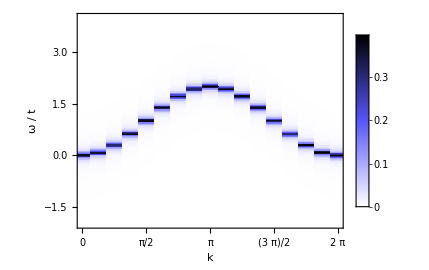

```mathematica
spcPlots
```

```mathematica
SavePlots[]:=(
Do[(
Do[(
Do[(
fileName=StringJoin["plots/",head,"/",
head,"_L=",ToString[spcAvail["size"][[iN]]],
"_J=",ToString[spcAvail["coupling"][[iJ]]],
"_B=",ToString[spcAvail["interaction"][[iB]]],
".jpg"];
Export[fileName,spcPlots[[iN,iJ,iB]],ImageResolution->300];
),{iB,Length[spcAvail["interaction"]//Normal]}]
),{iJ,Length[spcAvail["coupling"]//Normal]}]
),{iN,Length[spcAvail["size"]//Normal]}]
)
```

```mathematica
(*SavePlots[]*)
```